Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]; (*λ en um*)
ℏωAu=2 Pi c ℏ/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
aU=Transpose[{λAu,nAu}];
```

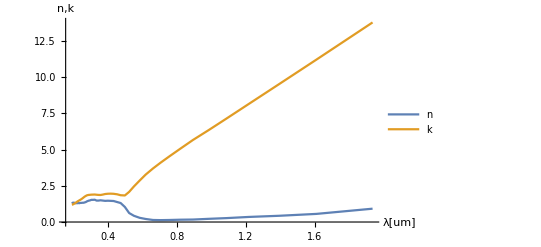

```mathematica
ListLinePlot[{Transpose[{λAu,nau}],Transpose[{λAu,kAu}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

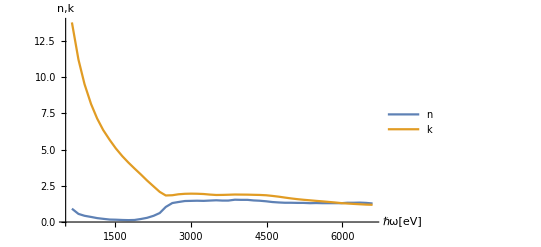

```mathematica
ListLinePlot[{Transpose[{ℏωAu,nau}],Transpose[{ℏωAu,kAu}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]];(*λ en um*)
ℏωAg=2 Pi c ℏ/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

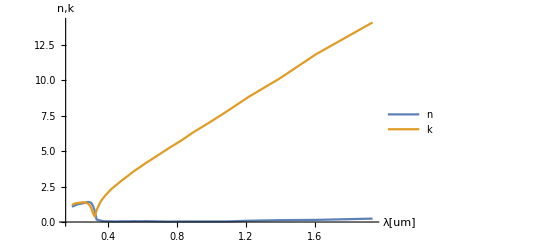

```mathematica
ListLinePlot[{Transpose[{λAg,nAg}],Transpose[{λAg,kAg}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

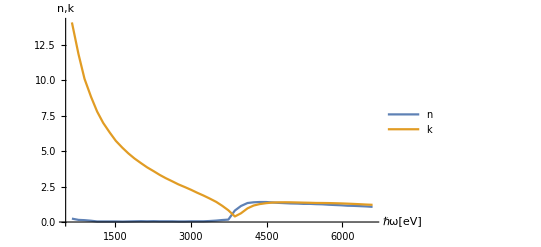

```mathematica
ListLinePlot[{Transpose[{ℏωAg,nAg}],Transpose[{ℏωAg,kAg}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]];(*λ en um*)
ℏωBism=2 Pi c ℏ/λBism; (*eV*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

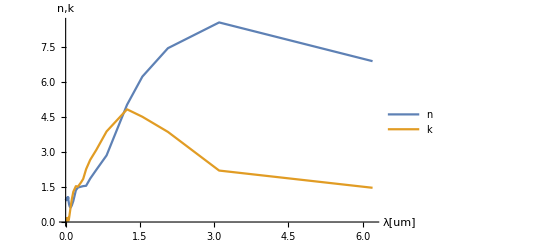

```mathematica
ListLinePlot[{Transpose[{λBism,nBis}],Transpose[{λBism,kBis}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

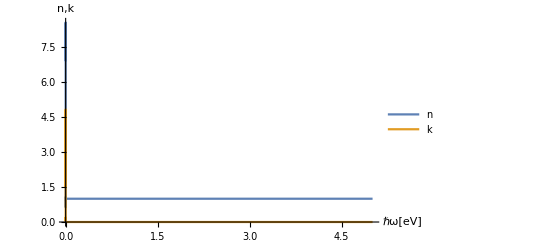

```mathematica
ListLinePlot[{Transpose[{ℏωBism,nBis}],Transpose[{ℏωBism,kBis}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]];(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

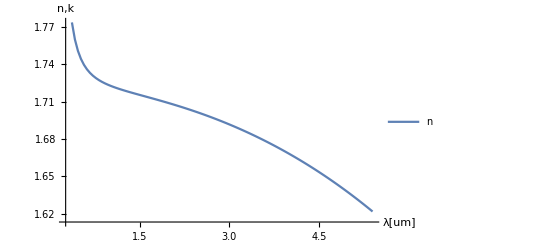

```mathematica
ListLinePlot[{Transpose[{λMgO,nMgO}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

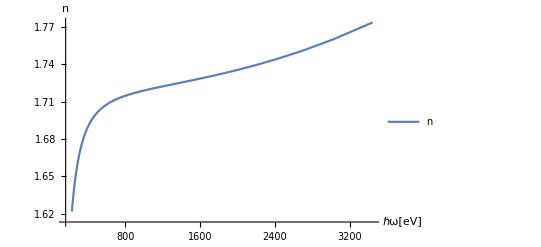

```mathematica
ListLinePlot[{Transpose[{ℏωMgO,nMgO}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n"},PlotLegends->{"n","k"}]
```

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

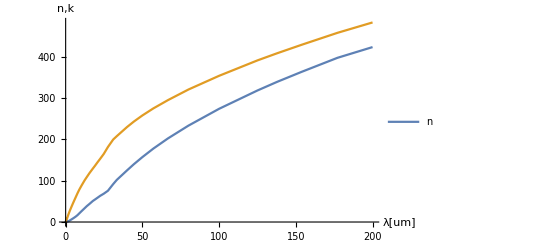

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

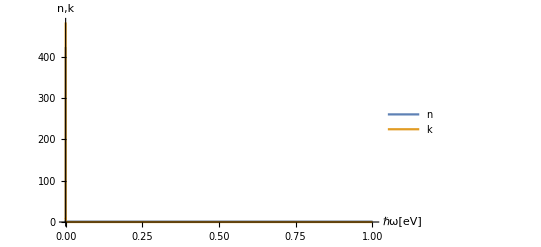

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```